```mathematica
A=({{-8, 3/4, -2}, {0, -2, 0}, {0, -3/2, -4}})
```

{{-8,3/4,-2},{0,-2,0},{0,-3/2,-4}}

```mathematica
λ=Eigenvalues[A]
```

{-8,-4,-2}

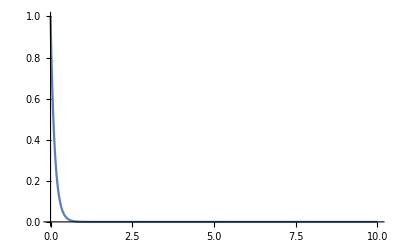

```mathematica
Plot[ⅇ^(-8t),{t,0,10},PlotRange->All]
```

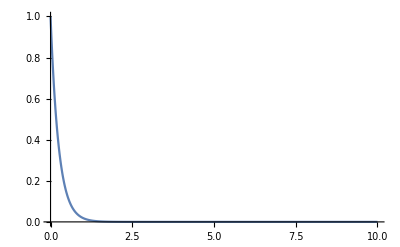

```mathematica
Plot[ⅇ^(-4t),{t,0,10},PlotRange->All]
```

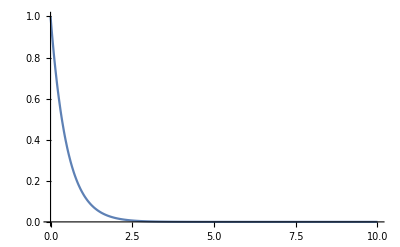

```mathematica
Plot[ⅇ^(-2t),{t,0,10},PlotRange->All]
```

```mathematica
N[Exp[-1]]
```

0.367879

```mathematica
T=Transpose[Eigenvectors[A]]
```

{{1,-1/2,-1/2},{0,0,-4/3},{0,1,1}}

```mathematica
T//MatrixForm
```

(1 | -1/2 | -1/2
0 | 0 | -4/3
0 | 1 | 1)

```mathematica
Subscript[x, 0]={{3},{-2},{0}}
```

{{3},{-2},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{3},{-3/2},{3/2}}

```mathematica
{n,n}=Dimensions[A]
```

{3,3}

```mathematica
Subscript[x, l][t_]:=∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)Subscript[z, 0][[i,1]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(3 ⅇ^(-8 t)+(3 ⅇ^(-4 t))/4-(3 ⅇ^(-2 t))/4
-2 ⅇ^(-2 t)
-3/2 ⅇ^(-4 t)+(3 ⅇ^(-2 t))/2)

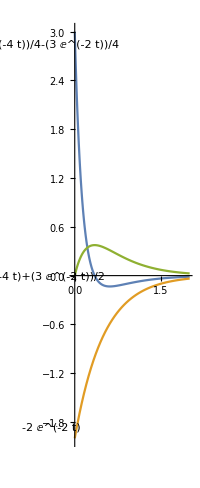

```mathematica
Plot[Evaluate[Subscript[x, l][t]],{t,0,2},PlotRange->All,AspectRatio->Automatic,PlotLabels->Placed[Automatic,Before]]
```

```mathematica
Subscript[x, 0]={{10},{0},{0}}
```

{{10},{0},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{10},{0},{0}}

```mathematica
Subscript[x, l][t_]:=∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)Subscript[z, 0][[i,1]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(10 ⅇ^(-8 t)
0
0)

```mathematica
Subscript[x, 0]={{-1},{-8/3},{2}}
```

{{-1},{-8/3},{2}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{0},{2}}

```mathematica
Subscript[x, l][t_]:=∑_(i=1)^n T[[All,i]] ⅇ^(λ[[i]]t)Subscript[z, 0][[i,1]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-ⅇ^(-2 t)
-8/3 ⅇ^(-2 t)
2 ⅇ^(-2 t))